## Some simple nonlinear oscillators

## Math 4354 Prof. Katharine Long

For most systems of nonlinear differential equations, it’s difficult if not impossible to find an exact solution. For autonomous equations, phase plots are easy to draw and can give insight into the solution’s behavior even without computing a solution.  
Here are a few examples:

The simple pendulum

The van der Pol oscillator

The bistable switch

## Phase plot for a pendulum

This is one of the simplest, but also deepest, nonlinear problems in mechanics. Equation of motion: x''+β x'+sin(x)=0. In the small-angle approximation this is the harmonic oscillator equation x''+β x' + x=0; when that approximation is not valid the dynamics becomes more complex and interesting. 

There are stable equilibrium points at (2n π,0) and unstable equilibrium points at ((2n+1)π,0).  There is an exact solution to the equation of motion (using Jacobi elliptic functions) only in the no-damping case β=0.

```mathematica
PENDULUM[β_,x_,y_]={y,-Sin[x]-β y}
```

{y,β (-y)-sin(x)}

#### View how the phase plot changes as the damping parameter β increases

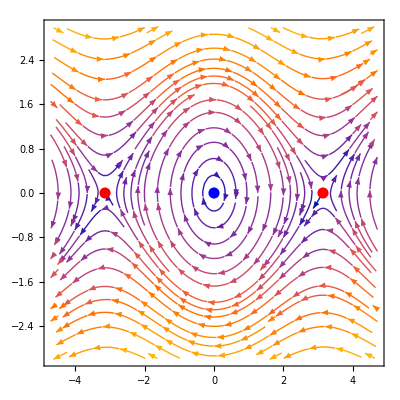

```mathematica
StreamPlot[PENDULUM[0,x,y],{x,-3/2Pi,3/2Pi},{y,-3,3},StreamPoints->Fine,
Epilog->{PointSize[0.02],Blue,Point[{0,0}],Red,Point[{Pi,0}],Point[{-Pi,0}]}]
```

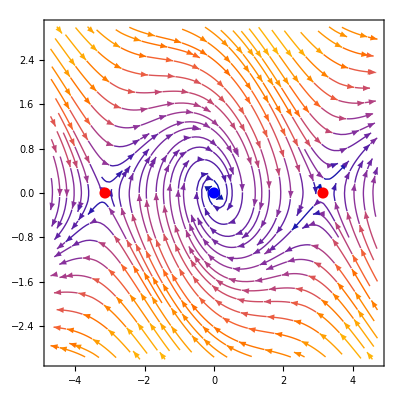

```mathematica
StreamPlot[PENDULUM[0.5,x,y],{x,-3/2Pi,3/2Pi},{y,-3,3},StreamPoints->Fine,
Epilog->{PointSize[0.02],Blue,Point[{0,0}],Red,Point[{Pi,0}],Point[{-Pi,0}]}]
```

```mathematica
Manipulate[StreamPlot[PENDULUM[β,x,y],{x,-3/2Pi,3/2Pi},{y,-3,3},StreamPoints->Fine,
Epilog->{PointSize[0.02],Blue,Point[{0,0}],Red,Point[{Pi,0}],Point[{-Pi,0}]}],{{β,0},0,2}]
```

## Phase plot for the Lotka-Volterra predator-prey model

```mathematica
LV[{p_,q_,r_,s_},x_,y_]={p x - q x y, -r y + s x y}
```

{p x-q x y,s x y-r y}

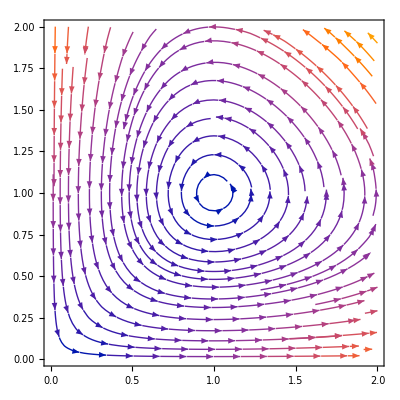

```mathematica
StreamPlot[LV[{1,1,1,1},x,y],{x,0,2},{y,0,2}]
```

## Phase plot for the van der Pol oscillator

The van der Pol oscillator is used to model steady, self-exciting oscillations in many fields of science including electrical engineering, neuroscience, and astronomy. The differential equation is x''-μ x'(1-x^2)+x=0. When μ=0 the equation is a simple harmonic oscillator with sinusoidal motion. With μ>0 the second term (which is nonlinear) produces damping for large x^2 but anti-damping for small x^2.

There is no known exact solution to the van der Pol equation, but approximate solutions can be computed in a number of ways including numerical integration.

```mathematica
VDP[μ_,x_,y_]={y,-x + μ(1-x^2)y}
```

{y,μ (1-x^2) y-x}

Vary the damping parameter μ  to see how the oscillator’s response changes. Notice that the origin becomes a repeller when μ>0; orbits near the origin spiral outwards. Notice also that orbits that start far from the origin spiral inwards. What happens in between?

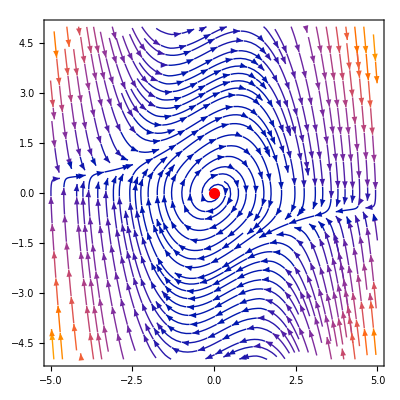

```mathematica
StreamPlot[VDP[0.5,x,y],{x,-5,5},{y,-5,5},
Epilog->{PointSize[0.02],Red,Point[{0,0}]},StreamPoints->Fine]
```

```mathematica
Manipulate[StreamPlot[VDP[μ,x,y],{x,-5,5},{y,-5,5},
Epilog->{PointSize[0.02],Red,Point[{0,0}]},StreamPoints->Fine],{{μ,0},0,2}]
```